# Transitive inference decision process as a linear network

## Under the hypothesis a relatively small threshold the OU process is well approximated by a Wiener process. Two absorbing barriers are taken into account (decision to move to left or to right).

Maurizio Mattia, December 2022, Rome - Italy

```mathematica
SetDirectory[NotebookDirectory[]];
```

### General solution of the Laplace transform γ(s,x_0) of the p.d.f. of the f.p.t.

```mathematica
Θp[s_]=(-μ+√(μ^2+2s σ^2))/σ^2
```

(-μ+√(μ^2+2 s σ^2))/σ^2

```mathematica
Θm[s_]=(-μ-√(μ^2+2s σ^2))/σ^2
```

(-μ-√(μ^2+2 s σ^2))/σ^2

```mathematica
γ[s_,x0_]=A Exp[x0 Θp[s]]+B Exp[x0 Θm[s]]
```

B ⅇ^((x0 (-μ-√(μ^2+2 s σ^2)))/σ^2)+A ⅇ^((x0 (-μ+√(μ^2+2 s σ^2)))/σ^2)

### Case of two symmetric absorbing barriers

#### Top barrier (a)

```mathematica
ABp=Simplify[Solve[γ[s,a]==1 && γ[s,-a]==0,{A,B}][[1]]]
```

{A→(ⅇ^((a (μ+3 √(μ^2+2 s σ^2)))/σ^2))/(-1+ⅇ^((4 a √(μ^2+2 s σ^2))/σ^2)),B→-(ⅇ^((a (μ+√(μ^2+2 s σ^2)))/σ^2))/(-1+ⅇ^((4 a √(μ^2+2 s σ^2))/σ^2))}

```mathematica
γp[s_,x0_]=FullSimplify[γ[s,x0]/.ABp]
```

ⅇ^(((a-x0) μ)/σ^2) Csch[(2 a √(μ^2+2 s σ^2))/σ^2] Sinh[((a+x0) √(μ^2+2 s σ^2))/σ^2]

#### Bottom barrier (-a)

```mathematica
ABm=Simplify[Solve[γ[s,a]==0 && γ[s,-a]==1,{A,B}][[1]]]
```

{A→-(ⅇ^((a (-μ+√(μ^2+2 s σ^2)))/σ^2))/(-1+ⅇ^((4 a √(μ^2+2 s σ^2))/σ^2)),B→(ⅇ^((a (-μ+3 √(μ^2+2 s σ^2)))/σ^2))/(-1+ⅇ^((4 a √(μ^2+2 s σ^2))/σ^2))}

```mathematica
γm[s_,x0_]=FullSimplify[γ[s,x0]/.ABm]
```

(-ⅇ^(((a+x0) (-μ+√(μ^2+2 s σ^2)))/σ^2)+ⅇ^(-(a (μ-3 √(μ^2+2 s σ^2))+x0 (μ+√(μ^2+2 s σ^2)))/σ^2))/(-1+ⅇ^((4 a √(μ^2+2 s σ^2))/σ^2))

## Case x_0 = 0

```mathematica
γp[s_]=FullSimplify[γp[s,0]]
```

1/2 ⅇ^((a μ)/σ^2) Sech[(a √(μ^2+2 s σ^2))/σ^2]

```mathematica
πp=FullSimplify[γp[0]]
```

1/2 (1+Tanh[(a μ)/σ^2])

```mathematica
InverseLaplaceTransform[γp[s],s,t]
```

ⅇ^((a μ)/σ^2) InverseLaplaceTransform[1/(ⅇ^(-(a √(μ^2+2 s σ^2))/σ^2)+ⅇ^((a √(μ^2+2 s σ^2))/σ^2)),s,t]

```mathematica
γm[s_]=FullSimplify[γm[s,0]]
```

1/2 ⅇ^(-(a μ)/σ^2) Sech[(a √(μ^2+2 s σ^2))/σ^2]

```mathematica
πm=FullSimplify[γm[0]]
```

1/(1+ⅇ^((2 a μ)/σ^2))

```mathematica
Simplify[πp+πm]
```

1

```mathematica
TP[μ_,σ_,a_]=πp
```

1/2 (1+Tanh[(a μ)/σ^2])

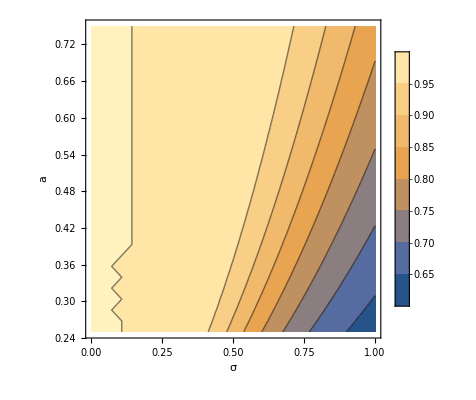

```mathematica
ContourPlot[TP[1,σ,a],{σ,0,1},{a,0.25,0.75},PlotLegends->Automatic,FrameLabel->{"σ","a"}]
```

What is the σ leading to the accuracy α for a given μ and “a”? As you can see it is proportional to √a, meaning that σ^2/a should be considered as a constant. In other words, changing “a” has no effect on TP and RT provided that they are function of σ^2/a.

```mathematica
Solve[πp==α,σ]
```

{{σ→ConditionalExpression[-(√a √μ)/(√(-ArcTanh[1-2 α]+ⅈ π C[1])), C[1]∈ℤ]},{σ→ConditionalExpression[(√a √μ)/(√(-ArcTanh[1-2 α]+ⅈ π C[1])), C[1]∈ℤ]}}

```mathematica
Sigma[α_,a_,μ_]=√((a μ)/ArcTanh[2α-1]);
```

How σ must be varied when threshold “a” changes to keep accuracy α constant.

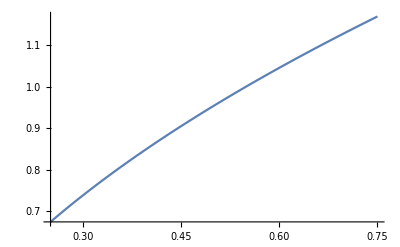

```mathematica
Module[{α=0.75,μ=1},
Plot[Sigma[α,a,μ],{a,0.25,0.75}]
]
```

This varying the threshold “a”.

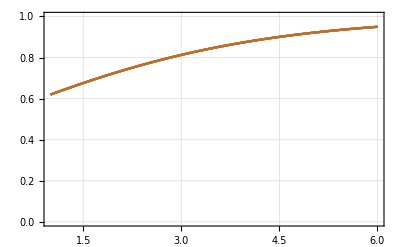

```mathematica
Module[{α1=0.62},
Plot[Evaluate[Table[TP[μ,Sigma[α1,a,1],a],{a,0.25,0.75,0.1}]],{μ,1,6},PlotRange->{0,1},Frame->True,GridLines->Automatic]
]
```

This varying the accuracy α1 at μ = 1.

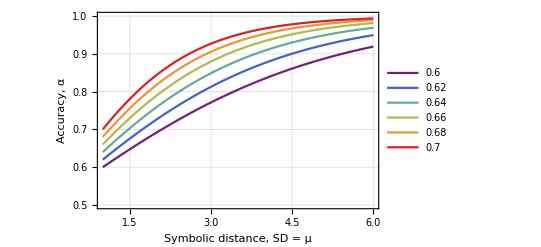

```mathematica
hgAcc=Module[{a=0.25},
Plot[Evaluate[Table[TP[μ,Sigma[α1,a,1],a],{α1,0.6,0.7,0.02}]],{μ,1,6},PlotRange->{0.5,1},Frame->True,GridLines->Automatic,FrameLabel->{"Symbolic distance, SD = μ","Accuracy, α"},PlotLegends->Table[α1,{α1,0.6,0.7,0.02}],PlotStyle->Table[ColorData["Rainbow"][x],{x,0,1,0.2}]]
]
```

```mathematica
Table[Sigma[α,0.25,1],{α,0.6,0.7,0.02}]
```

{1.11047,1.01062,0.93221,0.868224,0.814451,0.768187}

```mathematica
Export["AccurarcyVsSDvaryingNoise.png",hgAcc,ImageResolution->200];
```

```mathematica
Export["AccurarcyVsSDvaryingNoise.pdf",hgAcc,ImageResolution->200];
```

The following expression is for the normalized reaction time for the True Positives.

```mathematica
ReactionTime[μ_,σ_,a_]=FullSimplify[-γp'[0]/πp]
```

(a Tanh[(a μ)/σ^2])/μ

```mathematica
ReactionTime[1,σ,a]
```

a Tanh[a/σ^2]

```mathematica
ReactionTime[μ,σ,a]/ReactionTime[1,σ,a]
```

(Coth[a/σ^2] Tanh[(a μ)/σ^2])/μ

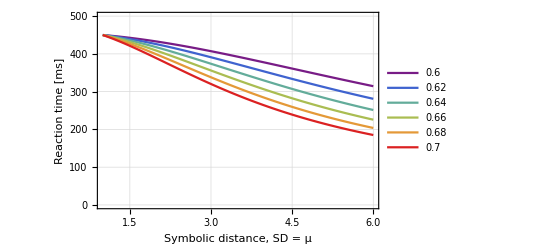

```mathematica
hgRT=Module[{a=0.25,RT1=450},
Plot[Evaluate[Table[RT1 ReactionTime[μ,Sigma[α1,a,1],a]/ReactionTime[1,Sigma[α1,a,1],a],{α1,0.6,0.7,0.02}]],{μ,1,6},PlotRange->{0,500},Frame->True,GridLines->Automatic,FrameLabel->{"Symbolic distance, SD = μ","Reaction time [ms]"},PlotLegends->Table[α1,{α1,0.6,0.7,0.02}],PlotStyle->Table[ColorData["Rainbow"][x],{x,0,1,0.2}]]
]
```

```mathematica
Export["RtvsSDvaryingNoise.png",hgRT,ImageResolution->200];
```

```mathematica
Export["RtvsSDvaryingNoise.pdf",hgRT,ImageResolution->200];
```

In what follows the so-called “anchor effect” is plotted:

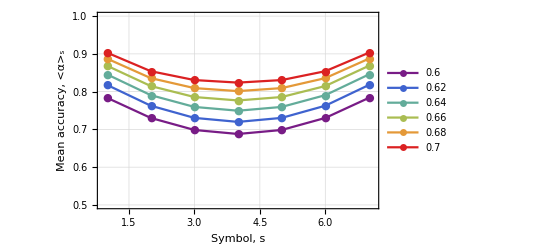

```mathematica
hgAF=Module[{a=0.25,α1=0.7,NoS=7,MeanAccuracy},
MeanAccuracy[S_,α1_,NoS_]:=1/(NoS-1)∑_(s=1)^NoS If[S≠s,TP[Abs[S-s],Sigma[α1,a,1],a],0];
ListPlot[Evaluate[Table[Table[MeanAccuracy[S,α1,NoS],{S,NoS}],{α1,0.6,0.7,0.02}]],
PlotRange->{{0.9,NoS+0.1},{0.5,1}},Frame->True,GridLines->Automatic,FrameLabel->{"Symbol, s","Mean accuracy, <α>_s"},Joined->True,PlotMarkers->"●",PlotLegends->Table[α1,{α1,0.6,0.7,0.02}],PlotStyle->Table[ColorData["Rainbow"][x],{x,0,1,0.2}]]
]
```

```mathematica
Export["AnchorEffectVaryingNoise.png",hgAF,ImageResolution->200];
```

```mathematica
Export["AnchorEffectVaryingNoise.pdf",hgAF,ImageResolution->200];
```

### Taking into account both the directional and thermal noise (σD and σT, respectively).

```mathematica
∫_(-∞)^∞ ReactionTime[x,σT,a]PDF[NormalDistribution[μ,σD],x]ⅆx
```

∫_(-∞)^∞ (a ⅇ^(-(x-μ)^2/(2 σD^2)) Tanh[(a x)/σT^2])/(√(2 π) x σD)ⅆx

```mathematica
FullSimplify[Series[ReactionTime[μ,σT,a],{μ,SD,2}]]
```

(a Tanh[(a SD)/σT^2])/SD+(a (a SD Sech[(a SD)/σT^2]^2-σT^2 Tanh[(a SD)/σT^2]) (μ-SD))/(SD^2 σT^2)+(a (σT^4 Tanh[(a SD)/σT^2]-a SD Sech[(a SD)/σT^2]^2 (σT^2+a SD Tanh[(a SD)/σT^2])) (μ-SD)^2)/(SD^3 σT^4)+O[μ-SD]^3

```mathematica
RT[SD_,σT_,σD_,a_]=Assuming[{σD∈Reals&& σD>0},∫_(-∞)^∞ Normal[Series[ReactionTime[μ,σT,a],{μ,SD,2}]] PDF[NormalDistribution[SD,σD],μ]ⅆμ]
```

(a Sech[(a SD)/σT^2]^2 ((SD^2+σD^2) σT^4 Sinh[(2 a SD)/σT^2]-2 a SD σD^2 (σT^2+a SD Tanh[(a SD)/σT^2])))/(2 SD^3 σT^4)

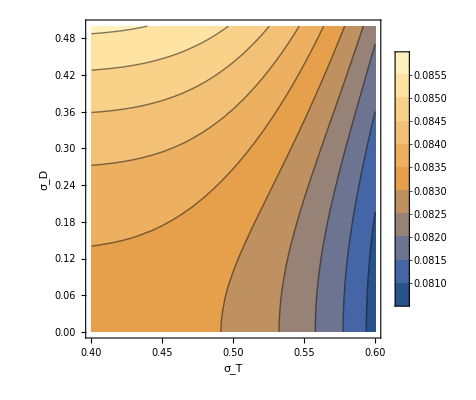

```mathematica
Module[{a=0.25,μ=3,RT1=450},
ContourPlot[RT[μ,σT,σD,a],{σT,0.4,0.6},{σD,0.0,0.5},PlotLegends->Automatic,FrameLabel->{"σ_T","σ_D"}]
]
```

```mathematica
Collect[%,σD]
```

(a Sech[(a SD)/σT^2]^2 Sinh[(2 a SD)/σT^2])/(2 SD)+(a σD^2 Sech[(a SD)/σT^2]^2 (σT^4 Sinh[(2 a SD)/σT^2]-2 a SD (σT^2+a SD Tanh[(a SD)/σT^2])))/(2 SD^3 σT^4)

```mathematica
FullSimplify[%]
```

(a Sech[(a SD)/σT^2]^2 ((SD^2+σD^2) σT^4 Sinh[(2 a SD)/σT^2]-2 a SD σD^2 (σT^2+a SD Tanh[(a SD)/σT^2])))/(2 SD^3 σT^4)

```mathematica
FullSimplify[(a Sech[(a SD)/σT^2]^2 Sinh[(2 a SD)/σT^2])/(2 SD)]
```

(a Tanh[(a SD)/σT^2])/SD

```mathematica
FullSimplify[Out[28]-%]
```

-(a σD^2 (-σT^4 Tanh[(a SD)/σT^2]+a SD Sech[(a SD)/σT^2]^2 (σT^2+a SD Tanh[(a SD)/σT^2])))/(SD^3 σT^4)

### Density of the first-passage time (FPT) of a Wiener process with an absorbing barrier at a (just for illustrative purpose).

```mathematica
FPTdensity[t_,μ_,σ_,a_]=a/(σ √(2π t^3))Exp[-(a-μ t)^2/(2 σ^2 t)]
```

(a ⅇ^(-(a-t μ)^2/(2 t σ^2)))/(√(2 π) √(t^3) σ)

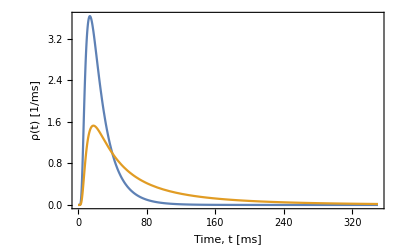

```mathematica
Module[{τ=100,tmax=350,a=0.8,σ=(3 √2)/4},
hp=Plot[{FPTdensity[t/τ,3,σ,a],FPTdensity[t/τ,1,σ,a]},{t,0,tmax},PlotRange->All,Frame->True,FrameLabel->{"Time, t [ms]","ρ(t) [1/ms]"}]
]
```

```mathematica
Export["FPTdensity.pdf",hp,ImageResolution->200];
```